# Numerical methods for ⅈ u_t+1/2 u_xx+|u|^2 u=0 on a<x<b with periodic BC.

## Method of Lines

We need to define the points at which we are going to approximate solutions.   We need to approximate the pieces in the PDE we want to solve using these values.  Approximating derivatives from sampled values!

```mathematica
Clear[D2s,D1c,D1f,D1b,D2w,D2v,Δx,h,n]
D2s[Δx_,n_]:=Δx^-2*SparseArray[{
Band[{1,1}]->-2.0,
Band[{1,2}]->1.0,
Band[{2,1}]->1.0,
{1,n}->1.0,{n,1}->1.0},{n,n}];
D1c[Δx_,n_]:=(2 Δx)^-1 SparseArray[{
Band[{2,1}]->-1.0,
Band[{1,2}]->1.0,
{1,n}->-1.0,{n,1}->1.0},{n,n}];
D1f[Δx_,n_]:=(Δx)^-1 SparseArray[{
Band[{1,1}]->1.0,
Band[{2,1}]->-1.0,
{1,n}->-1.0},{n,n}];
D1b[Δx_,n_]:=(Δx)^-1 SparseArray[{
Band[{1,1}]->-1.0,
Band[{1,2}]->1.0,
{n,1}->1.0},{n,n}];
D2w[Δx_,n_]:=(12 Δx^2)^-1*SparseArray[{
Band[{1,1}]->-30.0,
Band[{1,2}]->16.0,
Band[{2,1}]->16.0,
Band[{1,3}]->-1.0,
Band[{3,1}]->-1.0,
Band[{1,n}]->16.0,
Band[{n,1}]->16.0,
Band[{1,n-1}]->-1.0,
Band[{n-1,1}]->-1.0
},{n,n}];
D2v[Δx_,n_]:=(180 Δx^2)^-1*SparseArray[{
Band[{1,1}]->-490.0,
Band[{1,2}]->270.0,
Band[{2,1}]->270.0,
Band[{1,3}]->-27.0,
Band[{3,1}]->-27.0,
Band[{1,4}]->2.0,
Band[{4,1}]->2.0,
Band[{1,n}]->270.0,
Band[{n,1}]->270.0,
Band[{1,n-1}]->-27.0,
Band[{n-1,1}]->-27.0,
Band[{1,n-2}]->2.0,
Band[{n-2,1}]->2.0
},{n,n}];
n=10;
TabView[{
"D2s"->MatrixForm[D2s[h,n]],
"D1c"->MatrixForm[D1c[h,n]],
"D1f"->MatrixForm[D1f[h,n]],
"D1b"->MatrixForm[D1b[h,n]],
"D2w"->MatrixForm[D2w[h,n]],
"D2v"->MatrixForm[D2v[h,n]]
}]
```

123456

```mathematica
L=12;
{a,b}={-L,L};
n=2*512;
Δx=2.0 L/n;
x[j_]:= a+ Δx j
f[x_]:=2+1.2 Sin[3 π x/L]-0.4 Cos[2 π x/L]+3.2Sin[5 π x/L]
fVec=Table[f[x[j]],{j,1,n}];
D1fVec=Table[f'[x[j]],{j,1,n}];
D2fVec=Table[f''[x[j]],{j,1,n}];
TabView[{
"f"->Show[Plot[f[x],{x,a,b},PlotStyle->Red],
ListPlot[fVec,DataRange->{a+Δx,b}]],
"f'"->Show[Plot[f'[x],{x,a,b},PlotStyle->Red],
ListPlot[D1c[Δx,n].fVec,DataRange->{a+Δx,b}]],
"f''"->Show[Plot[f''[x],{x,a,b},PlotStyle->Red],
ListPlot[D2s[Δx,n].fVec,DataRange->{a+Δx,b}]],
"|f'-D_(1?).f|" -> ListLogPlot[ 
Abs[{D1fVec-D1c[Δx,n].fVec,D1fVec-D1b[Δx,n].fVec,D1fVec-D1f[Δx,n].fVec}],
DataRange->{-L,L},PlotLegends->{"c","b","f","orig"},GridLines->Automatic,
PlotRange->All],
"|f''-D_(2?).f|" -> ListLogPlot[ 
Abs[{D2fVec-D2s[Δx,n].fVec,D2fVec-D2w[Δx,n].fVec,D2fVec-D2v[Δx,n].fVec}],
DataRange->{-L,L},PlotRange->All,PlotLegends->{"s","w","v"},GridLines->Automatic]
}]
```

12345

We need to understand (in as many ways as possible) the effects of our different approximate differentiation matrices.

Here is what a MOL formulation looks like for the heat equation
	u_t=u_xx with u(x,0)=f(x)
on the interval {a,b} with periodic boundary conditions.  Approximate the solution at the spatial points
	x_j=a+j Δx
with Δx=(b-a)/n  and assemble the approximations
	u_j(t)≈u(a+j Δx,t)
into  the vector u(t)=(u_1(t),…,u_n(t)) the approximate the second derivative operator with your choice of the second derivative matrices. You get 
	u'=D_2.u  and u(0)=(f(x_1),f(x_2),…,f(x_n))

```mathematica
L=12;{a,b}={-L,L};
n=2*128;
Δx=2.0 L/n;
x[j_]:= a+ Δx j
f[x_]:=2+1.2 Sin[3 π x/L]-0.4 Cos[2 π x/L]+3.2Sin[5 π x/L]
u0=Table[ f[x[j]],{j,1,n}];
D2=D2v[Δx,n];
TMax=3;
uSol=NDSolveValue[{u'[t]==D2.u[t],u[0]==u0},u,{t, 0, TMax}]
TSteps=50;
Data=Table[uSol[t],{t,0, TMax, TMax/TSteps}];
ListPlot3D[Data,PlotRange->All];
```

InterpolatingFunction[{{0., 3.}}, <>]

```mathematica
TSteps=100;
Data=Table[uSol[t],{t,0, TMax, TMax/TSteps}];
Dimensions[Data];
TabView[{
"3d"->ListPlot3D[Data,PlotRange->All,
AxesLabel->{"x","t","u"},DataRange->{{-L,L},{0,TMax}}],
"Contours"->ListContourPlot[Data,PlotRange->All,
FrameLabel->{"x","t"},DataRange->{{-L,L},{0,TMax}},
PlotLegends->Automatic]
}]
```

12

## Spectral Methods

We need to understand and check the Fourier solvers for linear PDEs.  The first thing we need to understand is the order that our FFT puts the pieces in.   We decided we are doing a periodic problem on the interval -L<x<L.  We are going to assume our data is of length n with x_1=-L+Δx, x_2=-L+2 Δx, and x_n=-L+n Δx=L

```mathematica
FourierShift[data_?ArrayQ]:=FourierShift[data,All]
FourierShift[data_?ArrayQ,dim_]:=Block[
  {n=ConstantArray[0,ArrayDepth@data]},
  n[[dim]]=Check[
      Ceiling[Dimensions[data]/2][[dim]],
      Return[data,Block]
  ];
  RotateLeft[data,n]
]
```

```mathematica
TabView[{
"Sin"->Plot[ {Sin[ π x/L],Sin[2 π x/L],Sin[3 π x/L],Sin[4 π x/L]},{x,-L,L},
PlotLegends->{1,2,3,4}],
"Cos"->Plot[ {Cos[ π x/L],Cos[2 π x/L],Cos[3 π x/L],Cos[4 π x/L]},{x,-L,L},
PlotLegends->{1,2,3,4}]
}]
```

12

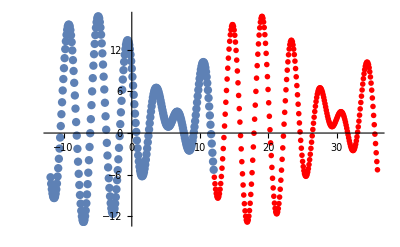

```mathematica
L=12;
m=128;n=2*m;
Δx=2.0L/n;
f[x_]:=2+ 7.3 Cos[5π x/L]-7.7 Sin[6π x/L]
x[j_]:=-L+j Δx
fVec=Table[f[x[j]],{j,1,n}];
Show[
ListPlot[fVec,
PlotStyle->PointSize[0.015],
DataRange->{-L+Δx,L}],
ListPlot[fVec,PlotStyle->Directive[PointSize[0.01],Red],
DataRange->{L+Δx,3L}],
PlotRange->All
]
```

```mathematica
fHat=Fourier[fVec];
NewfHat=FourierShift[fHat];
TabView[{
"orig"->ListPlot[{Re[fHat],Im[fHat],Abs[fHat]},
PlotLegends->{"re","im","abs"},PlotRange->All,
DataRange->{1,2m},GridLines->Automatic,PlotStyle->{PointSize[0.02],PointSize[0.015],PointSize[0.01]}],
"orig-zoom"->ListPlot[{Re[fHat],Im[fHat],Abs[fHat]},
PlotLegends->{"re","im","abs"},PlotRange->{{1,11},All},
DataRange->{1,2m},GridLines->Automatic,PlotStyle->{PointSize[0.02],PointSize[0.015],PointSize[0.01]}],
"new"->ListPlot[{Re[NewfHat],Im[NewfHat],Abs[NewfHat]},
PlotLegends->{"re","im"},PlotRange->All,PlotStyle->{PointSize[0.02],PointSize[0.015],PointSize[0.01]},
DataRange->{-m-1,m},GridLines->Automatic],
"new-Zoom"->ListPlot[{Re[NewfHat],Im[NewfHat],Abs[NewfHat]},
PlotLegends->{"re","im"},PlotRange->{{-10,10},All},PlotStyle->{PointSize[0.02],PointSize[0.015],PointSize[0.01]},
DataRange->{-m-1,m},GridLines->Automatic]
}]
```

1234